# ODVOD Kaj je odvod? Odvod v matematiki predstavlja spremembo funkcije pri spremembi njenega argumenta. Opisuje najboljši linearno aproksimacijo funkcije v bližni vrednosti funkcije z nekim argumentom. -Graphics-

# ODVOD FUNKCIJE

## odvod funkcije - v določeni točki je limita deferenčnega kvocienta Δy/Δx, ko gre Δx proti nič. geometrijski pomen odvod- vrednost odvoda funkcije v x0 je enaka smernemu koeficientu tangente na graf funkcije v točki z absciso x0 kot pod katerim seka krivulja os x - je enak naklonskemu kotu tangente na krivuljo v presečišču z osjo x. kot pod katerim krivulja seka os x - je enak kotu med tangentama na obe krivulji v njunem presečišču

PRAVILA ZA ODVAJANJE: 
Odvod konstante funkcije                                                  (c ’) = 0 
Odvod potenčne funkcije                                                              (x^n)' = n* x^(n - 1)
Odvod vsote funkcij                                                              ( f + g)’ = f ’ + g ’
Odvod zmnožka dveh funkcij                                          (f ’ × g’) = f ’ × g + f × g ’
Odvod zmnožka funkcije s konstantno funkcijo    (c × f)’ = c × f ’
Odvod količnika dveh funkcij                                          (f/g)' = (f ' * g - f* g')/g^2

1. NALOGA - določi enačbo tangente na graf x^2+ y^2= 1, x =1/2

```mathematica
Solve[(1/2)^2+y^2 ==1]
```

{{y→-(√3)/2},{y→(√3)/2}}

```mathematica
Solve[D[x^2+y[x]^2==1,x],y'[x]]/.{x->1/2,y[x]->(√3)/2}
```

{{y'[1/2]→-1/(√3)}}

```mathematica
Solve[(√3)/2==-1/3*(1/2)+ b,b]
```

{{b→1/6 (1+3 √3)}}

WolframAlphaQueryParseResults

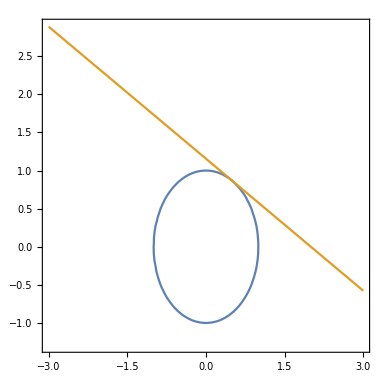

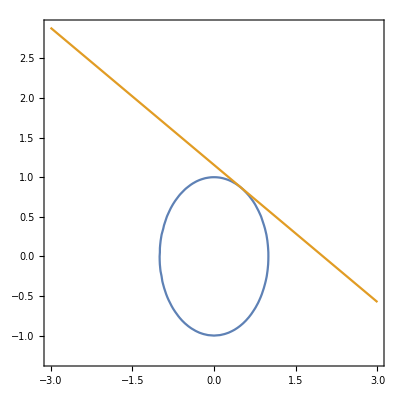

```mathematica
Show[%1,Axes->True,AxesStyle->Gray]
```

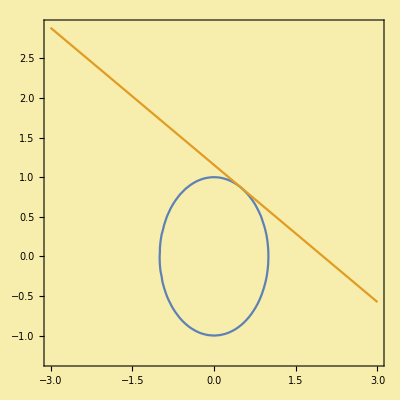

```mathematica
Show[%2,Background->RGBColor[0.97,0.93,0.68]]
```

2. NALOGA - Nariši graf sin(x), nato pa naredi še prvi in drugi odvod in jih nariši na grafu.

```mathematica
f[g_] := Sin[g]
f[π/3]
```

(√3)/2

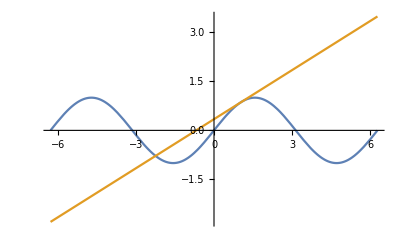

```mathematica
L[g_] := f[π/3] + f'[π/3] * (g - π/3)

Plot[{f[g],L[g]}, {g, -2π, 2π}]
```

```mathematica
Manipulate [Plot[{f[g], L[g]}, {g, π/3 +h, π/3 - h}, PlotRange->{(√3)/2 - h, (√3)/2 +h}], {h, 5, .01}]
```

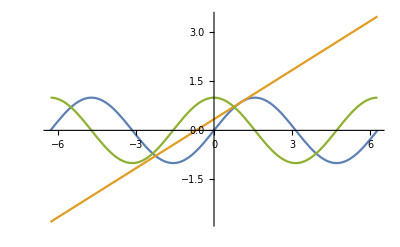

```mathematica
Plot[{f[g],L[g], f'[g]},  {g, -2π, 2π}]
```

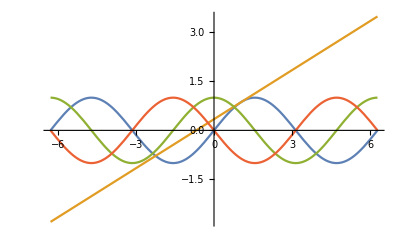

```mathematica
Plot[{f[g],L[g], f'[g], f''[g]},  {g, -2π, 2π}]
```

3.NALOGA - pokaži, da y = 6 x^3+5x +6 nima naklona pri 4

```mathematica
f[x_]:= 6 x^3+5x -3
f'[x]
```

5+18 x^2

```mathematica
Solve[f'[x] == 4]
```

{{x→-ⅈ/(3 √2)},{x→ⅈ/(3 √2)}}

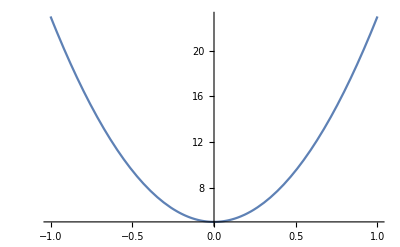

```mathematica
Plot[f'[x],{x, -1, 1}]
```

4. NALOGA Odvajaj funkcijo f(x) = ⅇ^x in nariši graf.

```mathematica
f[x_] := E^x
f'[x]
```

ⅇ^x

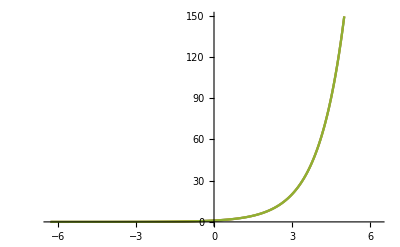

```mathematica
Plot[{f[x], f'[x], f''[x]}, {x, -2π, +2π}]
```

5.NALOGA funkciji f(x) = x + 2Sin x na intervalu [0, 2π] določite maksimum in minimum.

```mathematica
f[x_] := x + 2Sin[x]
PLot [f[x], {x, 0 , 2π}]
```

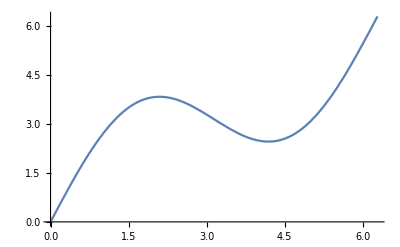

```mathematica
Plot[f[x],{x,0,2 π}]
```

```mathematica
Solve [f'[x] == 0, x]
```

```mathematica
{{x->ConditionalExpression[-(2 π)/3+2 π C[1],C[1]∈Integers]},{x->ConditionalExpression[(2 π)/3+2 π C[1],C[1]∈Integers]}}
Reduce[f'[x] == 0 && 0  ≤ x ≤ 2π, x]
```

{{x→ConditionalExpression[-(2 π)/3+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[(2 π)/3+2 π C[1],C[1]∈ℤ]}}

x==(2 π)/3||x==(4 π)/3

```mathematica
FindRoot[f'[x] == 0, {x, 0, 2π}]
```

{x→4.18879}

```mathematica
seznam = {0, 2π/3, 4π/3, 2π}
```

{0,(2 π)/3,(4 π)/3,2 π}

```mathematica
f[seznam]
```

{0,√3+(2 π)/3,-√3+(4 π)/3,2 π}

```mathematica
N[f[seznam] ]
```

{0.,3.82645,2.45674,6.28319}

### 6. NALOGA : Odvaja funkcijo f(x) = x^2+2x+1 in nariši graf odvod in prvotne funkcije.

```mathematica
f[x_] := x^2 + 2x + 1
f'[x]
```

2+2 x

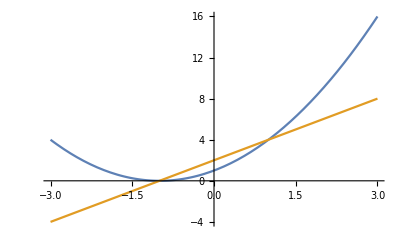

```mathematica
Plot [{f[x], f'[x]}, {x, -3, 3}]
```